```mathematica
AppendTo[$Path, NotebookDirectory[]];
```

```mathematica
AbsOxyHemo = Import["AbsorbanceOxyHemo.csv"];
AbsDeOxyHemo = Import["AbsorbanceDeOxyHemo.csv"];
AbsMel= Import["AbsorbanceMel.csv"];
```

```mathematica
showSpectrumResponse[spectrum_]:=Show[DensityPlot[x, {x, 380, 720}, {y, 0, 1}, ColorFunction -> ColorData["VisibleSpectrum"], ColorFunctionScaling -> False, 
   AspectRatio -> 1], 
  Plot[{spectrum[1, "Func"][λ], spectrum[2, "Func"][λ], spectrum[3, "Func"][λ]}, 
   {λ, 380, 720}, PlotRange -> All, ColorFunction -> (spectrum["ColorFunction"][#1] & ), 
   ColorFunctionScaling -> False, PlotStyle -> {Directive[Thick, Red], Directive[Thick, Green], Directive[Thick, Blue]}, 
   Filling -> Axis], 
Plot[{spectrum[1, "Func"][λ], spectrum[2, "Func"][λ], spectrum[3, "Func"][λ]}, 
   {λ, 380, 720}, PlotRange -> All, PlotStyle -> {Directive[Thick, Darker[Red]], Directive[Thick, Darker[Green]], Directive[Thick, Darker[Blue]]}],
ListPlot[{spectrum[1], spectrum[2], spectrum[3]}, PlotRange -> All, 
   PlotStyle -> {Red, Green, Blue}],FrameLabel->{{"Response",None},{"λ     nm" ,spectrum["name"]}},ImageSize->400]
```

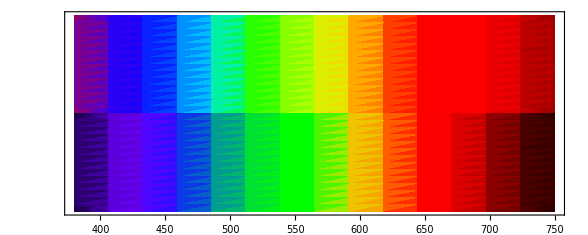

```mathematica
Show[DensityPlot[x,{x,380,750},{y,25,50},ColorFunction->(RGBColor@@toRGB[#1]&),ColorFunctionScaling->False,PlotRange->{All,{0,50}}],DensityPlot[x,{x,380,750},{y,0,25},ColorFunction->ColorData["VisibleSpectrum"],ColorFunctionScaling->False,PlotRange->{All,{0,50}}],AspectRatio->Automatic,PlotRangePadding->10,FrameTicks->{{None,None},{Automatic,None}}]
```

```mathematica
showWavelengthColor[list_]:= 
Graphics[{EdgeForm[Gray],Table[{ColorData["VisibleSpectrum"][list[[t]]],Disk[{t,0},.4],Black,Text[list[[t]]"λ",{t,0},{-1,0},{0,1}]},{t,1,Length[list]}]}]
```

```mathematica
OxyHemoglobin={415,540,570};
DeoxyHemoglobin={430,555};
```

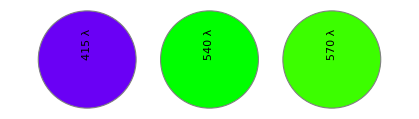

```mathematica
showWavelengthColor[OxyHemoglobin]
```

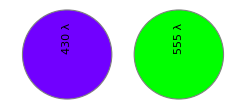

```mathematica
showWavelengthColor[DeoxyHemoglobin]
```

```mathematica
OxyHemoglobinRGB = Transpose[Map[toRGB,OxyHemoglobin]]
DeoxyHemoglobinRGB = Transpose[Map[toRGB,DeoxyHemoglobin]]
```

{{0.158333,3/7,6/7},{0,1,1},{1,0,0}}

{{0.0633333,9/14},{0,1},{1,0}}

```mathematica
nYAB[-0.1537].OxyHemoglobinRGB + {{0,0,0},{0.5,0.5,0.5},{0.5,0.5,0.5}}
```

{{0.193056,0.238095,0.309524},{0.846045,0.0783929,0.156786},{0.161267,0.632185,0.846471}}

## Response Spectra

```mathematica
ResponseSpectra={};
```

### Physical Spectrum

```mathematica
toRGB[wavelength_]:=Piecewise[{{{0.6 - 0.41(wavelength-380)/30,0,0.39 + 0.6(wavelength-380)/30},wavelength ≥ 380.0 && wavelength ≤ 410.0},{{0.19 - 0.19(wavelength-410)/30,0,1},wavelength ≥ 410.0 && wavelength ≤ 440.0},{{0,1 - (490-wavelength)/50,1},wavelength ≥ 440.0 && wavelength ≤ 490.0},{{0,1,(510-wavelength)/20},wavelength ≥ 490.0 && wavelength ≤ 510.0},{{1 - (580-wavelength)/70,1,0},wavelength ≥ 510.0 && wavelength ≤ 580.0},
{{1,(640-wavelength)/60,0},wavelength ≥ 580.0 && wavelength ≤ 640.0},
{{1,0,0},wavelength ≥ 640.0 && wavelength ≤ 700.0},
{{0.35 + 0.65(780-wavelength)/80,0,0},wavelength ≥ 700.0 && wavelength ≤ 780.0}}]
```

```mathematica
approxPhysical["name"]="Approximate Physical Spectrum";
Do[
approxPhysical[i,"Func"]     =Function[{λ},Evaluate[ApplyToPiecewise[#[[i]]&,toRGB[λ]]]];
approxPhysical[i]= Table[{i,physical[i,"Func"][i]},{i,300,780}]
,{i,1,3}];
approxPhysical["ColorFunction"]= Function[{λ},RGBColor[toRGB[λ]]];
```

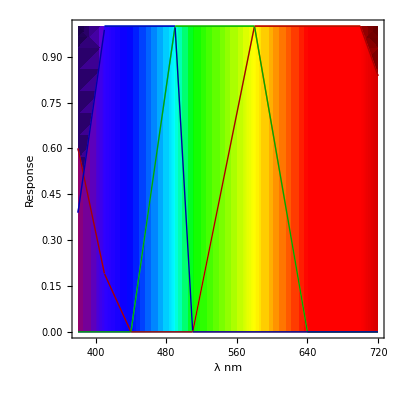

```mathematica
showSpectrumResponse[approxPhysical]
```

```mathematica
AppendTo[ResponseSpectra,physical];
```

{physical}

```mathematica
physical["name"]="Physical Spectrum";
Do[
physical[i,"Func"]     =Function[{λ},(List@@ColorData["VisibleSpectrum"][λ])[[j]]]/.j->i;
physical[i]= Table[{j,physical[i,"Func"][j]},{j,300,780}];
physical[i,"Func"]=Interpolation[physical[i]]
,{i,1,3}];
physical["ColorFunction"]= ColorData["VisibleSpectrum"];
```

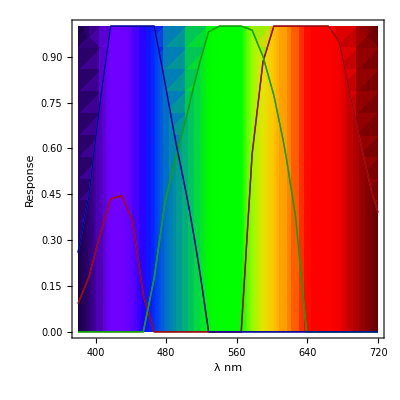

```mathematica
showSpectrumResponse[physical]
```

### The human Eye

```mathematica
AppendTo[ResponseSpectra,eye];
σRGB={60,60,60}; μRGB ={580,530,450};
gaussian[λ_,μ_,σ_]:= Exp[-(λ-μ)^2/(2*σ^2)];
eye["name"]="Response Spectrum for the human eye";
eye[3]= Import["EyeRGB_Blue_Gaussian.csv"];
eye[2]= Import["EyeRGB_Green_Gaussian.csv"];
eye[1]= Import["EyeRGB_Red_Gaussian.csv"];
Do[
{σRGB[[i]],μRGB[[i]]}={σ,μ}/.FindFit[eye[i],gaussian[λ,μ,σ],{{σ,σRGB[[i]]},{ μ, μRGB[[i]]}},λ];
eye[i,"Func"]     =Function[{λ}, Evaluate[gaussian[λ,μRGB[[i]],σRGB[[i]]]]];
,{i,1,3}];
eye["ColorFunction"]=RGBColor[eye[1,"Func"][#],eye[2,"Func"][#],eye[3,"Func"][#]]&;
```

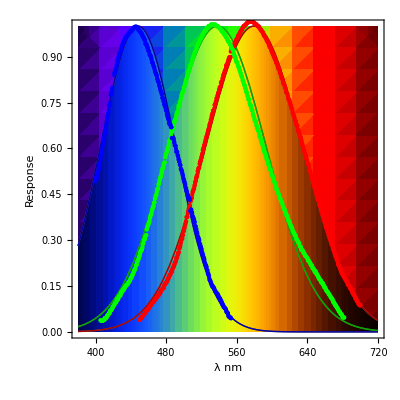

```mathematica
showSpectrumResponse[eye]
```

## Digital Camera Response Spectra

```mathematica
camData= Import["camspec_database.csv"];
```

```mathematica
scalePoints[list_,scale_]:=Block[{tran},tran=Transpose[list];Transpose[{scale[[1]] tran[[1]],scale[[2]] tran[[2]]}]];
```

```mathematica
camspecDatabaseλ=Table[λ,{λ,400,720,10}];
```

```mathematica
Do[
sym     = ToExpression[           StringReplace[camData[[n,1]], {" " -> "","-"->""}]]; 
symNorm = ToExpression[StringJoin[StringReplace[camData[[n,1]], {" " -> "","-"->""}],"Norm"]];
AppendTo[ResponseSpectra,sym]; AppendTo[ResponseSpectra,symNorm];
sym["name"]     = StringJoin["Response Spectrum for the ",camData[[n,1]]];
symNorm["name"] = StringJoin["Normalized Response Spectrum for the ",camData[[n,1]]];
sym["Red"]   = sym[1]; sym["Green"] = sym[2]; sym["Blue"]  = sym[3];
Do[
sym[i]       = Prepend[Prepend[Transpose[{camspecDatabaseλ,camData[[n + i]]}],{390,0}],{380,0}];
sym[i,"max"] = sym[i][[Ordering[sym[i][[All,2]],-1][[1]]]];
symNorm[i]   = scalePoints[sym[i],{1,1/sym[i,"max"][[2]]}];
max = FindMaximum[Interpolation[symNorm[i]][λ],{λ, sym[i,"max"][[1]]}];
    sym[i,"Func"] = Interpolation[sym[i]];
symNorm[i,"Func"] = Interpolation[scalePoints[symNorm[i],{1,1/max[[1]]}]];
,{i,1,3}]; 
    sym["ColorFunction"] = Function[{λ},Evaluate[RGBColor[    sym[1,"Func"][λ],    sym[2,"Func"][λ],    sym[3,"Func"][λ]]]];
symNorm["ColorFunction"] = Function[{λ},Evaluate[RGBColor[symNorm[1,"Func"][λ],symNorm[2,"Func"][λ],symNorm[3,"Func"][λ]]]];
 , {n, 1, Length[camData], 4}]
```

```mathematica
cameraSpectrumResponseGraphs=Table[showSpectrumResponse[ResponseSpectra[[i]]],{i,1,Length[ResponseSpectra]}];
Grid[ArrayReshape[cameraSpectrumResponseGraphs,{Floor[N[Sqrt[Length[ResponseSpectra]]]],Ceiling[N[Sqrt[Length[ResponseSpectra]]]]}]]
```

-Graphics-

```mathematica
SpectrumStrips[spectrum_]:=Module[{min,max,yVals,ticks},
min=0;max=Length[spectrum];
yVals=Table[i,{i,min,max,(max-min)/Length[spectrum]}];ticks=Table[{(yVals[[j]]+ yVals[[j+1]])/2,ToString[spectrum[[j]]]},{j,1,Length[spectrum],1}];Show[Table[DensityPlot[x, {x, 380, 720}, {y, yVals[[i]], yVals[[i+1]]}, ColorFunction -> spectrum[[i]]["ColorFunction"], ColorFunctionScaling -> False, 
   AspectRatio -> 1,PlotRange->{{380,720},{min,max}},FrameTicks->{ {ticks,{}},{Automatic,None}},FrameLabel->{{None,None},{"λ     nm",None}}],{i,1,Length[spectrum],1}]]]
```

```mathematica
SpectrumStrips[ResponseSpectra[[1;;Length[ResponseSpectra];;2]]]
```

-Graphics-

```mathematica
SpectrumStrips[ResponseSpectra[[2;;Length[ResponseSpectra];;2]]]
```

-Graphics-

```mathematica
Grid[{{showSpectrumResponse[NokiaN900],showSpectrumResponse[NokiaN900Norm]}}]
```

-Graphics- | -Graphics-

## The Absorbtion Spectrum for Chromophores

```mathematica
hemoglobin["base"] = 10;
hemoglobin["chemical"] = "Hb";
hemoglobin["quantity"] = {Quantity[1, "Nanometers"], Quantity[1/10, "Meters"^2/"Moles"]};
hemoglobin["symbol"] = {"λ", TraditionalForm[ε]};
hemoglobin["units"] = {"nm", TraditionalForm["l"/("cm"*"mol")]};
hemoglobin["value"] = {"Wavelength", "Molar absorptivity"};
hemoglobin["data"] = {{250, 112736}, {252, 112736}, {254, 112736}, {256, 113824}, {258, 115040}, {260, 116296}, {262, 117564}, {264, 118876}, 
     {266, 120208}, {268, 121544}, {270, 122880}, {272, 123096}, {274, 121952}, {276, 120808}, {278, 119840}, {280, 118872}, {282, 117628}, 
     {284, 114820}, {286, 112008}, {288, 107140}, {290, 98364}, {292, 91636}, {294, 85820}, {296, 77100}, {298, 69444}, {300, 64440}, 
     {302, 61300}, {304, 58828}, {306, 56908}, {308, 57620}, {310, 59156}, {312, 62248}, {314, 65344}, {316, 68312}, {318, 71208}, {320, 74508}, 
     {322, 78284}, {324, 82060}, {326, 85592}, {328, 88516}, {330, 90856}, {332, 93192}, {334, 95532}, {336, 99792}, {338, 104476}, 
     {340, 108472}, {342, 110996}, {344, 113524}, {346, 116052}, {348, 118752}, {350, 122092}, {352, 125436}, {354, 128776}, {356, 132120}, 
     {358, 133632}, {360, 134940}, {362, 136044}, {364, 136972}, {366, 137900}, {368, 138856}, {370, 139968}, {372, 141084}, {374, 142196}, 
     {376, 143312}, {378, 144424}, {380, 145232}, {382, 145232}, {384, 148668}, {386, 153908}, {388, 159544}, {390, 167780}, {392, 180004}, 
     {394, 191540}, {396, 202124}, {398, 212712}, {400, 223296}, {402, 236188}, {404, 253368}, {406, 270548}, {408, 287356}, {410, 303956}, 
     {412, 321344}, {414, 342596}, {416, 363848}, {418, 385680}, {420, 407560}, {422, 429880}, {424, 461200}, {426, 481840}, {428, 500840}, 
     {430, 528600}, {432, 552160}, {434, 552160}, {436, 547040}, {438, 501560}, {440, 413280}, {442, 363240}, {444, 282724}, {446, 237224}, 
     {448, 173320}, {450, 103292}, {452, 62640}, {454, 36170}, {456, 30698.8}, {458, 25886.4}, {460, 23388.8}, {462, 20891.2}, {464, 19260.8}, 
     {466, 18142.4}, {468, 17025.6}, {470, 16156.4}, {472, 15310}, {474, 15048.4}, {476, 14792.8}, {478, 14657.2}, {480, 14550}, {482, 14881.2}, 
     {484, 15212.4}, {486, 15543.6}, {488, 15898}, {490, 16684}, {492, 17469.6}, {494, 18255.6}, {496, 19041.2}, {498, 19891.2}, {500, 20862}, 
     {502, 21832.8}, {504, 22803.6}, {506, 23774.4}, {508, 24745.2}, {510, 25773.6}, {512, 26936.8}, {514, 28100}, {516, 29263.2}, 
     {518, 30426.4}, {520, 31589.6}, {522, 32851.2}, {524, 34397.6}, {526, 35944}, {528, 37490}, {530, 39036.4}, {532, 40584}, {534, 42088}, 
     {536, 43592}, {538, 45092}, {540, 46592}, {542, 48148}, {544, 49708}, {546, 51268}, {548, 52496}, {550, 53412}, {552, 54080}, {554, 54520}, 
     {556, 54540}, {558, 54164}, {560, 53788}, {562, 52276}, {564, 50572}, {566, 48828}, {568, 46948}, {570, 45072}, {572, 43340}, {574, 41716}, 
     {576, 40092}, {578, 38467.6}, {580, 37020}, {582, 35676.4}, {584, 34332.8}, {586, 32851.6}, {588, 31075.2}, {590, 28324.4}, {592, 25470}, 
     {594, 22574.8}, {596, 19800}, {598, 17058.4}, {600, 14677.2}, {602, 13622.4}, {604, 12567.6}, {606, 11513.2}, {608, 10477.6}, {610, 9443.6}, 
     {612, 8591.2}, {614, 7762}, {616, 7344.8}, {618, 6927.2}, {620, 6509.6}, {622, 6193.2}, {624, 5906.8}, {626, 5620}, {628, 5366.8}, 
     {630, 5148.8}, {632, 4930.8}, {634, 4730.8}, {636, 4602.4}, {638, 4473.6}, {640, 4345.2}, {642, 4216.8}, {644, 4088.4}, {646, 3965.08}, 
     {648, 3857.6}, {650, 3750.12}, {652, 3642.64}, {654, 3535.16}, {656, 3427.68}, {658, 3320.2}, {660, 3226.56}, {662, 3140.28}, 
     {664, 3053.96}, {666, 2967.68}, {668, 2881.4}, {670, 2795.12}, {672, 2708.84}, {674, 2627.64}, {676, 2554.4}, {678, 2481.16}, 
     {680, 2407.92}, {682, 2334.68}, {684, 2261.48}, {686, 2188.24}, {688, 2115}, {690, 2051.96}, {692, 2000.48}, {694, 1949.04}, {696, 1897.56}, 
     {698, 1846.08}, {700, 1794.28}, {702, 1741}, {704, 1687.76}, {706, 1634.48}, {708, 1583.52}, {710, 1540.48}, {712, 1497.4}, {714, 1454.36}, 
     {716, 1411.32}, {718, 1368.28}, {720, 1325.88}, {722, 1285.16}, {724, 1244.44}, {726, 1203.68}, {728, 1152.8}, {730, 1102.2}, {732, 1102.2}, 
     {734, 1102.2}, {736, 1101.76}, {738, 1100.48}, {740, 1115.88}, {742, 1161.64}, {744, 1207.4}, {746, 1266.04}, {748, 1333.24}, 
     {750, 1405.24}, {752, 1515.32}, {754, 1541.76}, {756, 1560.48}, {758, 1560.48}, {760, 1548.52}, {762, 1508.44}, {764, 1459.56}, 
     {766, 1410.52}, {768, 1361.32}, {770, 1311.88}, {772, 1262.44}, {774, 1213}, {776, 1163.56}, {778, 1114.8}, {780, 1075.44}, {782, 1036.08}, 
     {784, 996.72}, {786, 957.36}, {788, 921.8}, {790, 890.8}, {792, 859.8}, {794, 828.8}, {796, 802.96}, {798, 782.36}, {800, 761.72}, 
     {802, 743.84}, {804, 737.08}, {806, 730.28}, {808, 723.52}, {810, 717.08}, {812, 711.84}, {814, 706.6}, {816, 701.32}, {818, 696.08}, 
     {820, 693.76}, {822, 693.6}, {824, 693.48}, {826, 693.32}, {828, 693.2}, {830, 693.04}, {832, 692.92}, {834, 692.76}, {836, 692.64}, 
     {838, 692.48}, {840, 692.36}, {842, 692.2}, {844, 691.96}, {846, 691.76}, {848, 691.52}, {850, 691.32}, {852, 691.08}, {854, 690.88}, 
     {856, 690.64}, {858, 692.44}, {860, 694.32}, {862, 696.2}, {864, 698.04}, {866, 699.92}, {868, 701.8}, {870, 705.84}, {872, 709.96}, 
     {874, 714.08}, {876, 718.2}, {878, 722.32}, {880, 726.44}, {882, 729.84}, {884, 733.2}, {886, 736.6}, {888, 739.96}, {890, 743.6}, 
     {892, 747.24}, {894, 750.88}, {896, 754.52}, {898, 758.16}, {900, 761.84}, {902, 765.04}, {904, 767.44}, {906, 769.8}, {908, 772.16}, 
     {910, 774.56}, {912, 776.92}, {914, 778.4}, {916, 778.04}, {918, 777.72}, {920, 777.36}, {922, 777.04}, {924, 776.64}, {926, 772.36}, 
     {928, 768.08}, {930, 763.84}, {932, 752.28}, {934, 737.56}, {936, 722.88}, {938, 708.16}, {940, 693.44}, {942, 678.72}, {944, 660.52}, 
     {946, 641.08}, {948, 621.64}, {950, 602.24}, {952, 583.4}, {954, 568.92}, {956, 554.48}, {958, 540.04}, {960, 525.56}, {962, 511.12}, 
     {964, 495.36}, {966, 473.32}, {968, 451.32}, {970, 429.32}, {972, 415.28}, {974, 402.28}, {976, 389.288}, {978, 374.944}, {980, 359.656}, 
     {982, 344.372}, {984, 329.084}, {986, 313.796}, {988, 298.508}, {990, 283.22}, {992, 267.932}, {994, 252.648}, {996, 237.36}, 
     {998, 222.072}, {1000, 206.784}};
```

```mathematica
oxyHemoglobin["base"] = 10;
oxyHemoglobin["chemical"] = "Hb02";
oxyHemoglobin["quantity"] = {Quantity[1, "Nanometers"], Quantity[1/10, "Meters"^2/"Moles"]};
oxyHemoglobin["symbol"] = {"λ", TraditionalForm[ε]};
oxyHemoglobin["units"] = {"nm", TraditionalForm["l"/("cm"*"mol")]};
oxyHemoglobin["value"] = {"Wavelength", "Molar absorptivity"};
oxyHemoglobin["data"] = {{250, 106112}, {252, 105552}, {254, 107660}, {256, 109788}, {258, 112944}, {260, 116376}, {262, 120188}, 
     {264, 124412}, {266, 128696}, {268, 133064}, {270, 136068}, {272, 137232}, {274, 138408}, {276, 137424}, {278, 135820}, {280, 131936}, 
     {282, 127720}, {284, 122280}, {286, 116508}, {288, 108484}, {290, 104752}, {292, 98936}, {294, 88136}, {296, 79316}, {298, 70884}, 
     {300, 65972}, {302, 63208}, {304, 61952}, {306, 62352}, {308, 62856}, {310, 63352}, {312, 65972}, {314, 69016}, {316, 72404}, 
     {318, 75536}, {320, 78752}, {322, 82256}, {324, 85972}, {326, 89796}, {328, 93768}, {330, 97512}, {332, 100964}, {334, 103504}, 
     {336, 104968}, {338, 106452}, {340, 107884}, {342, 109060}, {344, 110092}, {346, 109032}, {348, 107984}, {350, 106576}, {352, 105040}, 
     {354, 103696}, {356, 101568}, {358, 97828}, {360, 94744}, {362, 92248}, {364, 89836}, {366, 88484}, {368, 87512}, {370, 88176}, 
     {372, 91592}, {374, 95140}, {376, 98936}, {378, 103432}, {380, 109564}, {382, 116968}, {384, 125420}, {386, 135132}, {388, 148100}, 
     {390, 167748}, {392, 189740}, {394, 212060}, {396, 231612}, {398, 248404}, {400, 266232}, {402, 284224}, {404, 308716}, {406, 354208}, 
     {408, 422320}, {410, 466840}, {412, 500200}, {414, 524280}, {416, 521880}, {418, 515520}, {420, 480360}, {422, 431880}, {424, 376236}, 
     {426, 326032}, {428, 283112}, {430, 246072}, {432, 214120}, {434, 165332}, {436, 132820}, {438, 119140}, {440, 102580}, {442, 92780}, 
     {444, 81444}, {446, 76324}, {448, 67044}, {450, 62816}, {452, 58864}, {454, 53552}, {456, 49496}, {458, 47496}, {460, 44480}, 
     {462, 41320}, {464, 39807.2}, {466, 37073.2}, {468, 34870.8}, {470, 33209.2}, {472, 31620}, {474, 30113.6}, {476, 28850.8}, {478, 27718}, 
     {480, 26629.2}, {482, 25701.6}, {484, 25180.4}, {486, 24669.6}, {488, 24174.8}, {490, 23684.4}, {492, 23086.8}, {494, 22457.6}, 
     {496, 21850.4}, {498, 21260}, {500, 20932.8}, {502, 20596.4}, {504, 20418}, {506, 19946}, {508, 19996}, {510, 20035.2}, {512, 20150.4}, 
     {514, 20429.2}, {516, 21001.6}, {518, 22509.6}, {520, 24202.4}, {522, 26450.4}, {524, 29269.2}, {526, 32496.4}, {528, 35990}, 
     {530, 39956.8}, {532, 43876}, {534, 46924}, {536, 49752}, {538, 51712}, {540, 53236}, {542, 53292}, {544, 52096}, {546, 49868}, 
     {548, 46660}, {550, 43016}, {552, 39675.2}, {554, 36815.2}, {556, 34476.8}, {558, 33456}, {560, 32613.2}, {562, 32620}, {564, 33915.6}, 
     {566, 36495.2}, {568, 40172}, {570, 44496}, {572, 49172}, {574, 53308}, {576, 55540}, {578, 54728}, {580, 50104}, {582, 43304}, 
     {584, 34639.6}, {586, 26600.4}, {588, 19763.2}, {590, 14400.8}, {592, 10468.4}, {594, 7678.8}, {596, 5683.6}, {598, 4504.4}, {600, 3200}, 
     {602, 2664}, {604, 2128}, {606, 1789.2}, {608, 1647.6}, {610, 1506}, {612, 1364.4}, {614, 1222.8}, {616, 1110}, {618, 1026}, {620, 942}, 
     {622, 858}, {624, 774}, {626, 707.6}, {628, 658.8}, {630, 610}, {632, 561.2}, {634, 512.4}, {636, 478.8}, {638, 460.4}, {640, 442}, 
     {642, 423.6}, {644, 405.2}, {646, 390.4}, {648, 379.2}, {650, 368}, {652, 356.8}, {654, 345.6}, {656, 335.2}, {658, 325.6}, {660, 319.6}, 
     {662, 314}, {664, 308.4}, {666, 302.8}, {668, 298}, {670, 294}, {672, 290}, {674, 285.6}, {676, 282}, {678, 279.2}, {680, 277.6}, 
     {682, 276}, {684, 274.4}, {686, 272.8}, {688, 274.4}, {690, 276}, {692, 277.6}, {694, 279.2}, {696, 282}, {698, 286}, {700, 290}, 
     {702, 294}, {704, 298}, {706, 302.8}, {708, 308.4}, {710, 314}, {712, 319.6}, {714, 325.2}, {716, 332}, {718, 340}, {720, 348}, 
     {722, 356}, {724, 364}, {726, 372.4}, {728, 381.2}, {730, 390}, {732, 398.8}, {734, 407.6}, {736, 418.8}, {738, 432.4}, {740, 446}, 
     {742, 459.6}, {744, 473.2}, {746, 487.6}, {748, 502.8}, {750, 518}, {752, 533.2}, {754, 548.4}, {756, 562}, {758, 574}, {760, 586}, 
     {762, 598}, {764, 610}, {766, 622.8}, {768, 636.4}, {770, 650}, {772, 663.6}, {774, 677.2}, {776, 689.2}, {778, 699.6}, {780, 710}, 
     {782, 720.4}, {784, 730.8}, {786, 740}, {788, 748}, {790, 756}, {792, 764}, {794, 772}, {796, 786.4}, {798, 807.2}, {800, 816}, 
     {802, 828}, {804, 836}, {806, 844}, {808, 856}, {810, 864}, {812, 872}, {814, 880}, {816, 887.2}, {818, 901.6}, {820, 916}, {822, 930.4}, 
     {824, 944.8}, {826, 956.4}, {828, 965.2}, {830, 974}, {832, 982.8}, {834, 991.6}, {836, 1001.2}, {838, 1011.6}, {840, 1022}, 
     {842, 1032.4}, {844, 1042.8}, {846, 1050}, {848, 1054}, {850, 1058}, {852, 1062}, {854, 1066}, {856, 1072.8}, {858, 1082.4}, {860, 1092}, 
     {862, 1101.6}, {864, 1111.2}, {866, 1118.4}, {868, 1123.2}, {870, 1128}, {872, 1132.8}, {874, 1137.6}, {876, 1142.8}, {878, 1148.4}, 
     {880, 1154}, {882, 1159.6}, {884, 1165.2}, {886, 1170}, {888, 1174}, {890, 1178}, {892, 1182}, {894, 1186}, {896, 1190}, {898, 1194}, 
     {900, 1198}, {902, 1202}, {904, 1206}, {906, 1209.2}, {908, 1211.6}, {910, 1214}, {912, 1216.4}, {914, 1218.8}, {916, 1220.8}, 
     {918, 1222.4}, {920, 1224}, {922, 1225.6}, {924, 1227.2}, {926, 1226.8}, {928, 1224.4}, {930, 1222}, {932, 1219.6}, {934, 1217.2}, 
     {936, 1215.6}, {938, 1214.8}, {940, 1214}, {942, 1213.2}, {944, 1212.4}, {946, 1210.4}, {948, 1207.2}, {950, 1204}, {952, 1200.8}, 
     {954, 1197.6}, {956, 1194}, {958, 1190}, {960, 1186}, {962, 1182}, {964, 1178}, {966, 1173.2}, {968, 1167.6}, {970, 1162}, {972, 1156.4}, 
     {974, 1150.8}, {976, 1144}, {978, 1136}, {980, 1128}, {982, 1120}, {984, 1112}, {986, 1102.4}, {988, 1091.2}, {990, 1080}, {992, 1068.8}, 
     {994, 1057.6}, {996, 1046.4}, {998, 1035.2}, {1000, 1024}};
```

```mathematica
Clear[pheomelanin];
pheomelanin["molarMass"]=295;
pheomelanin["chemical"] = {"pheomelanin"};
pheomelanin["value"] ={"Wavelength","Molar Extinction coefficient"};
pheomelanin["symbol"] = {"λ", TraditionalForm[ε]}; 
pheomelanin["base"] = 10; 
pheomelanin["units"] = {"nm", TraditionalForm["l"/("mol"*"cm")]}; 
pheomelanin["quantity"] = {Quantity[1, "Nanometers"], Quantity[1, "Centimeters"^-1  ("Moles"/"Liters")^-1]};
pheomelanin["data"] = {{213.54, 13922}, {217.92, 13611}, {222.25, 13198}, {226.55, 12732}, {228.59, 12268}, {232.91, 11854}, {234.95, 11389}, 
    {241.54, 10975}, {243.61, 10562}, {247.96, 10200}, {250.18, 10096}, {256.82, 9785.1}, {263.41, 9370.7}, {270.05, 9059.7}, {276.71, 8800.1}, 
    {285.6, 8436.7}, {292.24, 8125.8}, {298.88, 7814.5}, {303.26, 7503.9}, {312.08, 7037.5}, {323.18, 6570.5}, {334.25, 6052.2}, 
    {343.05, 5534.2}, {351.88, 5067.8}, {360.76, 4704.4}, {376.38, 4236.5}, {387.5, 3820.8}, {403.2, 3507.6}, {418.85, 3091.}, {430.04, 2830.2}, 
    {443.45, 2465.9}, {459.17, 2204.2}, {481.61, 1785.9}, {501.83, 1471.5}, {524.32, 1156.1}, {549.09, 892.08}, {591.91, 468.76}, 
    {600.98, 518.02}, {625.84, 408.58}, {652.98, 350.17}, {675.59, 292.93}, {700.47, 235.11}, {720.81, 178.48}, {750.22, 119.47}, 
    {770.62, 165.79}, {786.44, 110.33}, {802.28, 106.5}, {820.37, 50.15}, {829.42, 48.085}};
```

```mathematica
addSpectrumData[pheomelanin]
```

```mathematica
Clear[eumelanin];
eumelanin["molarMass"]=178;
eumelanin["chemical"] = {"eumelanin"};
eumelanin["value"] ={"Wavelength","Mass Extinction coefficient"};
eumelanin["symbol"] = {"λ", TraditionalForm[ε]}; 
eumelanin["base"] = 10; 
eumelanin["units"] = {"nm", TraditionalForm["l"/("mol"*"cm")]}; 
eumelanin["quantity"] = {Quantity[1, "Nanometers"], Quantity[1, "Centimeters"^-1  ("Moles"/"Liters")^-1]};
eumelanin["data"] = {{209.99, 7458.2}, {212.21, 7238.7}, {218.91, 6956.6}, {223.36, 6611.8}, {230.06, 6298.2}, {239., 5953.2}, {245.7, 5608.2}, {261.38, 5231.8}, 
  {279.3, 4855.3}, {294.99, 4510.2}, {312.92, 4196.4}, {324.13, 4008.}, {342.06, 3662.9}, {357.75, 3317.7}, {382.42, 2941.1}, {407.07, 2470.3}, 
  {431.74, 2125.}, {458.67, 1810.8}, {483.36, 1590.8}, {523.76, 1245.1}, {550.7, 1024.9}, {588.87, 804.56}, {615.82, 709.86}, {642.77, 583.84}, 
  {680.96, 488.79}, {712.41, 394.09}, {734.88, 362.05}, {764.09, 330.01}, {782.06, 298.15}, {804.53, 266.29}, {820.26, 265.93}};
```

```mathematica
addSpectrumData[eumelanin]
```

```mathematica
Grid[{{PlotSpectrum[eumelanin],PlotSpectrum[eumelanin,3],PlotSpectrum[eumelanin,4]},{PlotSpectrum[pheomelanin],PlotSpectrum[pheomelanin,3],PlotSpectrum[pheomelanin,4]}}]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

#### Kubelka - Munk theory

```mathematica
eqn1=r==K/S
eqn2=r==FullSimplify[((1+R^2 -T^2)/(2R))-1]
eqn3=S==FullSimplify[(1/d)(r(r+2))^(-1/2) ArcCoth[(1-R(r+1))/(R(r(r+2))^(1/2))]]
```

r==K/S

r==((-1+R)^2-T^2)/(2 R)

S==ArcTanh[(√(r (2+r)) R)/(1-(1+r) R)]/(d √(r (2+r)))

At visible wavelengths the transittance of skin T is approximately zero

```mathematica
K/S==(R - 1)^2/(2 R)
```

```mathematica
Assuming[Element[R,Reals]&& R≥0&&Element[r,Reals]&& r≥0,Solve[r==(R - 1)^2/(2 R),R]]
```

{{R→1+r-√(2 r+r^2)},{R→1+r+√(2 r+r^2)}}

```mathematica
Plot[{1+r+√(2 r+r^2),1+r-√(2 r+r^2)},{r,0,1}]
```

-Graphics-

as r is K/S the remission R must go down with increasing adsorbsion K.

```mathematica
remittance[r_]:=1+r-√(2 r+r^2)
```

#### Blood Constants

```mathematica
HbConcentration = Quantity[150,"Grams"]/Quantity[1,"Liters"]
HbMolarMass = UnitSimplify[ Quantity[64500,"Grams"]/Quantity[1,"Moles"]]
```

150

64500

```mathematica
Print["Typically in human blood Hb concentration is ",QuantityForm[N[HbConcentration],"LongForm"]]
Print["The molar mass of Hb is ",QuantityForm[N[HbMolarMass],"LongForm"]]
```

Typically in human blood Hb concentration is 150. grams per liter

The molar mass of Hb is 64500. grams per mole

```mathematica
HbConcentration /HbMolarMass
```

1/430

```mathematica
UnitConvert[HbConcentration /HbMolarMass,"Moles"/"Meters"^3]
```

100/43

```mathematica
UnitSimplify
```

```mathematica
absorbance[ε_,conc_:HbConcentration,molarMass_:HbMolarMass]:=UnitSimplify[ε conc /molarMass]
SetAttributes[absorbance,Listable]
```

#### Add Quantity info to the distributions

```mathematica
Clear[addData];
addData[{λ_,ε_},spectrum_,conc_:HbConcentration,molarMass_:HbMolarMass]:= Module[{wave,mec,abs,rem},
{wave,mec}=spectrum["quantity"] [[{1,2}]]{λ,ε};
abs=absorbance[mec,conc,molarMass];
rem = N[remittance[QuantityMagnitude[abs]]];
UnitSimplify[{wave,mec,abs,rem}]]
```

```mathematica
addSpectrumData[spectrum_] := Block[{},
spectrum["quantityData"] = 
   Map[(addData[#1, spectrum] & ), spectrum["data"]];
spectrum["value"] ={"Wavelength","Molar absorptivity","Absorption coefficient","Remittance"};
spectrum["symbol"] = {spectrum["symbol"][[1]], spectrum["symbol"][[2]], TraditionalForm[Subscript[µ,a]],"R"}; 
spectrum["quantity"] = {spectrum["quantity"][[1]], spectrum["quantity"][[2]], QuantityUnit[spectrum["quantityData"][[3,3]]],1}; 
]
```

```mathematica
addSpectrumData[hemoglobin];
```

```mathematica
addSpectrumData[oxyHemoglobin];
```

```mathematica
addSpectrumData[eumelanin];
```

```mathematica
addSpectrumData[pheomelanin];
```

### Visualize Spectrums

```mathematica
Clear[PlotSpectrum]
PlotSpectrum[spectrum_,n_:2,opts:OptionsPattern[]]:=ListLinePlot[QuantityMagnitude[spectrum["quantityData"][[All,{1,n}]]],PlotRange->All, Frame->True,AxesLabel-> Automatic,FrameLabel->{{Row[{spectrum["symbol"][[n]],"     ",If[unit=QuantityUnit[spectrum["quantityData"][[1,n]]];TrueQ[unit=="DimensionlessUnit"],"",QuantityForm[unit,"Abbreviation"]] }],None},{Row[{spectrum["symbol"][[1]],"     ",QuantityForm[QuantityUnit[spectrum["quantityData"][[1,1]]],"Abbreviation"] }],spectrum["chemical"]}}, ColorFunction->(ColorData["VisibleSpectrum"][ #]&),ColorFunctionScaling->False,Filling->Axis,TargetUnits->{"Nanometers",Automatic},Evaluate[FilterRules[{opts}, Options[ListLinePlot]]],ImageSize->400]
```

```mathematica
Grid[{{PlotSpectrum[hemoglobin],PlotSpectrum[hemoglobin,3],PlotSpectrum[hemoglobin,4]},{PlotSpectrum[oxyHemoglobin],PlotSpectrum[oxyHemoglobin,3],PlotSpectrum[oxyHemoglobin,4]},{PlotSpectrum[eumelanin],PlotSpectrum[eumelanin,3],PlotSpectrum[eumelanin,4]},{PlotSpectrum[pheomelanin],PlotSpectrum[pheomelanin,3],PlotSpectrum[pheomelanin,4]}}]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

### Restrict the Remittace spectrum to the visible wavelengths

```mathematica
Clear[restrictSpectrum,restrictSpectrumSet,wave,l,r,scale];
restrictSpectrumSet[out_,spectrum_,min_Quantity:Quantity[380,"Nanometers"],max_Quantity:Quantity[780,"Nanometers"]]:=Module[{},
wave=spectrum["quantityData"][[All,1]];
l=Position[wave,λ_/;λ>min,1,1][[1,1]];
r=Position[wave,λ_/;λ>max,1,1][[1,1]];
DownValues[out]=DownValues[spectrum]/.spectrum[n_]:> out[n];
out["quantityData"]=spectrum["quantityData"][[l;;r]];
scale=1/Max[out["quantityData"][[All,4]]];
out["quantityData"]=Transpose[{1,1,1,scale} Transpose[out["quantityData"]]];];
restrictSpectrum/: Set[sym_Symbol,restrictSpectrum[args__]]:= restrictSpectrumSet[sym,args]
```

```mathematica
Clear[hemoglobinVis]
hemoglobinVis=restrictSpectrum[hemoglobin,Quantity[380,"Nanometers"],Quantity[780,"Nanometers"]];
```

```mathematica
Clear[oxyHemoglobinVis]
oxyHemoglobinVis=restrictSpectrum[oxyHemoglobin,Quantity[380,"Nanometers"],Quantity[780,"Nanometers"]];
```

```mathematica
Clear[eumelaninVis]
eumelaninVis=restrictSpectrum[eumelanin,Quantity[380,"Nanometers"],Quantity[780,"Nanometers"]];
```

```mathematica
Clear[pheomelaninVis]
pheomelaninVis=restrictSpectrum[pheomelanin,Quantity[380,"Nanometers"],Quantity[780,"Nanometers"]];
```

```mathematica
Grid[{{PlotSpectrum[hemoglobinVis,4],PlotSpectrum[oxyHemoglobinVis,4]},{PlotSpectrum[eumelaninVis,4],PlotSpectrum[pheomelaninVis,4]}}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
hemoglobinVis["Func"]=Interpolation[QuantityMagnitude[hemoglobinVis["quantityData"][[All,{1,4}]]]];
oxyHemoglobinVis["Func"]=Interpolation[QuantityMagnitude[oxyHemoglobinVis["quantityData"][[All,{1,4}]]]];
eumelaninVis["Func"]=Interpolation[QuantityMagnitude[eumelaninVis["quantityData"][[All,{1,4}]]]];
pheomelaninVis["Func"]=Interpolation[QuantityMagnitude[pheomelaninVis["quantityData"][[All,{1,4}]]]];
```

```mathematica
Grid[{{
Plot[{NokiaN900Norm[1,"Func"][x],hemoglobinVis["Func"][x],NokiaN900Norm[1,"Func"][x]  hemoglobinVis["Func"][x]},{x,380,780}],Plot[{NokiaN900Norm[2,"Func"][x],hemoglobinVis["Func"][x],NokiaN900Norm[2,"Func"][x]  hemoglobinVis["Func"][x]},{x,380,780}],Plot[{NokiaN900Norm[3,"Func"][x],hemoglobinVis["Func"][x],NokiaN900Norm[3,"Func"][x]  hemoglobinVis["Func"][x]},{x,380,780}]},{Plot[{NokiaN900Norm[1,"Func"][x],oxyHemoglobinVis["Func"][x],NokiaN900Norm[1,"Func"][x]  oxyHemoglobinVis["Func"][x]},{x,380,780}],Plot[{NokiaN900Norm[2,"Func"][x],oxyHemoglobinVis["Func"][x],NokiaN900Norm[2,"Func"][x]  oxyHemoglobinVis["Func"][x]},{x,380,780}],Plot[{NokiaN900Norm[3,"Func"][x],oxyHemoglobinVis["Func"][x],NokiaN900Norm[3,"Func"][x]  oxyHemoglobinVis["Func"][x]},{x,380,780}]},{Plot[{NokiaN900Norm[1,"Func"][x],eumelaninVis["Func"][x],NokiaN900Norm[1,"Func"][x]  eumelaninVis["Func"][x]},{x,380,780}],Plot[{NokiaN900Norm[2,"Func"][x],eumelaninVis["Func"][x],NokiaN900Norm[2,"Func"][x]  eumelaninVis["Func"][x]},{x,380,780}],Plot[{NokiaN900Norm[3,"Func"][x],eumelaninVis["Func"][x],NokiaN900Norm[3,"Func"][x]  eumelaninVis["Func"][x]},{x,380,780}]},{Plot[{NokiaN900Norm[1,"Func"][x],pheomelaninVis["Func"][x],NokiaN900Norm[1,"Func"][x]  pheomelaninVis["Func"][x]},{x,380,780}],Plot[{NokiaN900Norm[2,"Func"][x],pheomelaninVis["Func"][x],NokiaN900Norm[2,"Func"][x]  pheomelaninVis["Func"][x]},{x,380,780}],Plot[{NokiaN900Norm[3,"Func"][x],pheomelaninVis["Func"][x],NokiaN900Norm[3,"Func"][x]  pheomelaninVis["Func"][x]},{x,380,780}]}}]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
remittanceToRGB[remittanceSpectrum_,responceSpectrum_]:=Module[{int},int={NIntegrate[responceSpectrum[1,"Func"][x]  remittanceSpectrum["Func"][x],{x,380,780}],NIntegrate[responceSpectrum[2,"Func"][x]  remittanceSpectrum["Func"][x],{x,380,780}],NIntegrate[responceSpectrum[3,"Func"][x]  remittanceSpectrum["Func"][x],{x,380,780}]};
(int -( Min[int]/3))/Max[int]]
```

```mathematica
setRGB[spectrum_]:=Map[Set[#["RGB",ToString[spectrum]],remittanceToRGB[#,spectrum]]&,{hemoglobinVis,oxyHemoglobinVis,eumelaninVis,pheomelaninVis}]
```

```mathematica
Map[setRGB,ResponseSpectra];
```

{{{0.959225,0.218806,0.0815505},{0.983689,0.200366,0.0326217},{0.904933,0.482981,0.190135},{0.938816,0.465622,0.122368}},{{0.907669,0.565498,0.184662},{0.96246,0.474781,0.0750803},{0.864926,0.706581,0.270149},{0.906674,0.682284,0.186651}},{{0.726899,0.751723,0.496553},{0.915613,0.432768,0.168775},{0.423709,0.816461,0.367077},{0.558121,0.854765,0.29047}},{{0.828419,0.411362,0.343162},{0.943129,0.237117,0.113743},{0.796306,0.732452,0.407388},{0.860841,0.669069,0.278319}},{{0.79521,0.682205,0.409581},{0.931756,0.399598,0.136489},{0.521205,0.839308,0.321383},{0.649124,0.873011,0.253978}},{{0.846101,0.364115,0.307799},{0.948715,0.221939,0.102571},{0.822907,0.679357,0.354186},{0.877039,0.62952,0.245922}},{{0.749441,0.614872,0.501118},{0.912433,0.345749,0.175134},{0.482753,0.765957,0.468086},{0.663927,0.812198,0.375604}},{{0.822962,0.430741,0.354077},{0.938128,0.242439,0.123745},{0.769295,0.749051,0.46141},{0.844204,0.668745,0.311592}},{{0.0421508,0.978925,0.776289},{0.832746,0.796675,0.334509},{0.21023,0.894885,0.471819},{0.224272,0.887864,0.349499}},{{0.0818472,0.959076,0.853554},{0.903374,0.399792,0.193251},{0.408219,0.79589,0.443092},{0.480607,0.82738,0.345239}},{{0.445822,0.777089,0.503565},{0.865075,0.609787,0.26985},{0.367017,0.816492,0.437083},{0.444004,0.826267,0.347467}},{{0.749653,0.648809,0.500694},{0.90672,0.354512,0.18656},{0.677721,0.762156,0.475688},{0.805565,0.778949,0.388871}},{{0.5193,0.754637,0.490726},{0.871396,0.578467,0.257209},{0.378674,0.810663,0.441829},{0.461221,0.823685,0.352629}},{{0.801853,0.553949,0.396294},{0.920585,0.327221,0.158831},{0.761768,0.774094,0.451813},{0.829221,0.731289,0.341557}},{{0.552179,0.797095,0.405809},{0.918549,0.540493,0.162902},{0.42154,0.843885,0.312229},{0.526672,0.875967,0.248066}},{{0.792208,0.585365,0.415585},{0.937016,0.309499,0.125968},{0.762957,0.798432,0.403136},{0.852604,0.77299,0.294792}},{{0.178996,0.910502,0.591825},{0.867159,0.756633,0.265683},{0.256024,0.871988,0.395416},{0.283003,0.859559,0.280882}},{{0.335854,0.832073,0.679849},{0.911904,0.385958,0.176192},{0.503471,0.782898,0.434204},{0.619762,0.825248,0.349504}},{{0.530955,0.783956,0.432089},{0.902984,0.560588,0.194033},{0.356147,0.821926,0.35807},{0.463251,0.856321,0.287359}},{{0.814613,0.54784,0.370775},{0.937813,0.297996,0.124375},{0.766203,0.790849,0.418301},{0.848255,0.750699,0.303489}},{{0.634638,0.658518,0.682681},{0.871345,0.38004,0.25731},{0.33494,0.83253,0.576157},{0.374797,0.812601,0.414006}},{{0.821808,0.356384,0.460824},{0.921737,0.187019,0.156526},{0.674262,0.710856,0.578287},{0.783086,0.710689,0.433828}},{{0.763541,0.721819,0.472918},{0.920193,0.400491,0.159614},{0.424799,0.813237,0.373526},{0.560123,0.851781,0.296439}},{{0.827973,0.499434,0.344053},{0.94194,0.278482,0.116121},{0.678882,0.806089,0.387821},{0.84777,0.836974,0.304461}},{{0.815423,0.566047,0.369155},{0.939811,0.312641,0.120378},{0.592044,0.823803,0.352393},{0.751733,0.86216,0.275681}},{{0.826811,0.42432,0.346378},{0.943525,0.240303,0.11295},{0.757415,0.792309,0.415382},{0.854609,0.749438,0.290781}},{{0.785375,0.59448,0.42925},{0.929996,0.322312,0.140008},{0.529868,0.810988,0.378024},{0.679781,0.851803,0.296394}},{{0.825763,0.411284,0.348475},{0.943169,0.227075,0.113662},{0.781349,0.787962,0.424075},{0.854695,0.72871,0.290611}},{{0.803716,0.507752,0.392567},{0.931481,0.292419,0.137039},{0.647233,0.793487,0.413027},{0.813107,0.835004,0.329992}},{{0.810215,0.40707,0.379569},{0.933749,0.239739,0.132501},{0.766118,0.759108,0.467763},{0.836896,0.703637,0.326209}},{{0.522085,0.759059,0.481883},{0.911979,0.4409,0.176041},{0.357415,0.821293,0.386579},{0.475503,0.853413,0.293175}},{{0.745362,0.63013,0.509277},{0.92902,0.286095,0.14196},{0.569059,0.774923,0.450153},{0.74638,0.824903,0.350195}},{{0.401204,0.799398,0.617175},{0.900342,0.438648,0.199315},{0.308357,0.845822,0.41694},{0.376747,0.85187,0.296261}},{{0.632826,0.683587,0.645192},{0.925706,0.266986,0.148588},{0.50571,0.776145,0.44771},{0.653715,0.825817,0.348366}},{{0.697917,0.745292,0.509415},{0.912018,0.422307,0.175964},{0.438004,0.80831,0.38338},{0.573672,0.844529,0.310943}},{{0.780683,0.561818,0.438634},{0.927832,0.307553,0.144336},{0.634915,0.788698,0.422603},{0.808485,0.828622,0.342756}},{{0.791222,0.595849,0.417556},{0.932528,0.32393,0.134945},{0.540514,0.811712,0.376577},{0.690612,0.853121,0.293759}},{{0.828808,0.435146,0.342385},{0.944675,0.239622,0.110651},{0.762258,0.795119,0.409763},{0.856193,0.755981,0.287614}},{{0.789427,0.620163,0.421146},{0.935848,0.328027,0.128303},{0.540892,0.836968,0.326065},{0.690668,0.871932,0.256136}},{{0.801706,0.446894,0.396587},{0.939589,0.244174,0.120821},{0.708686,0.802323,0.395355},{0.8527,0.801291,0.2946}},{{0.755615,0.61671,0.48877},{0.917002,0.340497,0.165996},{0.48286,0.789595,0.420809},{0.628008,0.831616,0.336768}},{{0.809147,0.415385,0.381706},{0.935183,0.233337,0.129635},{0.751315,0.766607,0.466785},{0.834881,0.718908,0.330238}},{{0.874896,0.442227,0.250208},{0.932409,0.309149,0.135182},{0.811724,0.752481,0.376552},{0.854603,0.700687,0.290793}},{{0.789027,0.421946,0.426937},{0.885117,0.305412,0.229767},{0.647909,0.69509,0.609821},{0.752872,0.696771,0.494255}},{{0.877422,0.415683,0.245157},{0.951061,0.26073,0.0978776},{0.825591,0.770812,0.348818},{0.877634,0.704286,0.244733}},{{0.843444,0.38419,0.313112},{0.937496,0.248594,0.125008},{0.777247,0.726832,0.445506},{0.843715,0.674184,0.31257}},{{0.415548,0.792226,0.480953},{0.90981,0.504382,0.18038},{0.327462,0.836269,0.347721},{0.422571,0.862511,0.274977}},{{0.659633,0.709657,0.580687},{0.925158,0.315284,0.149683},{0.532994,0.78439,0.431221},{0.67968,0.826119,0.347762}},{{0.866938,0.636236,0.266123},{0.940011,0.417702,0.119978},{0.676784,0.840262,0.319475},{0.802551,0.86736,0.265281}},{{0.82364,0.526083,0.35272},{0.920491,0.356668,0.159019},{0.684271,0.768134,0.463733},{0.812016,0.788389,0.375969}},{{0.927566,0.248783,0.144868},{0.950102,0.243438,0.0997954},{0.873116,0.328482,0.253768},{0.90402,0.335065,0.19196}},{{0.958845,0.3196,0.0823105},{0.971649,0.301091,0.0567013},{0.927908,0.439325,0.144185},{0.945467,0.429569,0.109067}},{{0.906834,0.186331,0.273039},{0.95087,0.122257,0.0982596},{0.810044,0.379912,0.460252},{0.855136,0.353612,0.289729}},{{0.925694,0.235831,0.148612},{0.970093,0.160269,0.059813},{0.868067,0.500409,0.263865},{0.911818,0.46494,0.176365}},{{0.793555,0.656243,0.412891},{0.915131,0.362466,0.169737},{0.69617,0.810254,0.379491},{0.844459,0.808216,0.311083}},{{0.763755,0.47249,0.673499},{0.877499,0.245003,0.25149},{0.690888,0.618225,0.634717},{0.771525,0.563292,0.45695}},{{0.209058,0.895471,0.630347},{0.858964,0.702991,0.282072},{0.244337,0.877831,0.434483},{0.27651,0.861745,0.310777}},{{0.351416,0.824292,0.762425},{0.892891,0.395006,0.214219},{0.410717,0.794642,0.505256},{0.506122,0.808924,0.382152}}}

```mathematica
showColor[remittanceSpectrum_,responceSpectrum_,{x_,y_}]:={RGBColor[remittanceSpectrum["RGB",ToString[responceSpectrum]]],Rectangle[{x,y},{x+1,y+1}],Black,Text[remittanceSpectrum["chemical"],{x+0.5,y+0.8}],Text[ToString[responceSpectrum],{x+0.5,y+0.65}],Text[Round[remittanceSpectrum["RGB",ToString[responceSpectrum]] 255],{x+0.5,y+0.5}]}
```

```mathematica
Graphics[Flatten[Table[{showColor[hemoglobinVis,ResponseSpectra[[i]],{0,i-1}],showColor[oxyHemoglobinVis,ResponseSpectra[[i]],{1,i-1}],showColor[eumelaninVis,ResponseSpectra[[i]],{2,i-1}],showColor[pheomelaninVis,ResponseSpectra[[i]],{3,i-1}]},{i,1,Length[ResponseSpectra]}]]]
```

-Graphics-

## Color matching functions

http://en.wikipedia.org/wiki/CIE_1931_color_space

```mathematica
αx = {0.364, 1.056, -0.065};
αy = {0.821, 0.286};
αz = {1.217, 0.681};

βx = {442.0, 599.8, 501.1};
βy = {568.8, 530.9};
βz = {437.0, 459.0};

γx = {0.0624, 0.0264, 0.0490};
γy = {0.0213, 0.0613};
γz = {0.0845, 0.0385};

δx = {0.0374, 0.0323, 0.0382};
δy = {0.0247, 0.0322};
δz = {0.0278, 0.0725};
norm=1;
funcs={
Function[{λ},Evaluate[Sum[αx[[i]] Exp[-1/2 ((λ - βx[[i]]) S[λ - βx[[i]],γx[[i]],δx[[i]]])^2],{i,1,3}]]],
Function[{λ},Evaluate[Sum[αy[[i]] Exp[-1/2 ((λ - βy[[i]]) S[λ - βy[[i]],γy[[i]],δy[[i]]])^2],{i,1,2}]]],
Function[{λ},Evaluate[Sum[αz[[i]] Exp[-1/2 ((λ - βz[[i]]) S[λ - βz[[i]],γz[[i]],δz[[i]]])^2],{i,1,2}]]]};
norm=Max[{FindMaximum[funcs[[1]][λ],{λ,600}][[1]],FindMaximum[funcs[[2]][λ],{λ,550}][[1]],FindMaximum[funcs[[3]][λ],{λ,450}][[1]]}];
```

```mathematica
norm=1;
S[x_,y_,z_]:= y(1-HeavisideTheta[x]) + z HeavisideTheta[x];
Clear[approxEye]
approxEye["name"]="Approximate Eye Spectrum";
approxEye[1,"Func"][λ_]:= Sum[αx[[i]] Exp[-1/2 ((λ - βx[[i]]) S[λ - βx[[i]],γx[[i]],δx[[i]]])^2],{i,1,3}]/norm
approxEye[2,"Func"][λ_]:= Sum[αy[[i]] Exp[-1/2 ((λ - βy[[i]]) S[λ - βy[[i]],γy[[i]],δy[[i]]])^2],{i,1,2}]/norm
approxEye[3,"Func"][λ_]:= Sum[αz[[i]] Exp[-1/2 ((λ - βz[[i]]) S[λ - βz[[i]],γz[[i]],δz[[i]]])^2],{i,1,2}]/norm
```

```mathematica
Do[
approxEye[i]= Table[{i,approxEye[i,"Func"][i]},{i,300,780}]
,{i,1,3}];
approxEye["ColorFunction"]= Function[{λ},RGBColor[approxEye[1,"Func"][λ],approxEye[2,"Func"][λ],approxEye[3,"Func"][λ]]];
```

```mathematica
showSpectrumResponse[approxEye]
```

-Graphics-

```mathematica
setRGB[approxEye];
```

```mathematica
Graphics[{showColor[hemoglobinVis,approxEye,{0,0}],showColor[oxyHemoglobinVis,approxEye,{1,0}],showColor[eumelaninVis,approxEye,{2,0}],showColor[pheomelaninVis,approxEye,{3,0}]}]
```

-Graphics-